## Custom Basis Vector Reduction

```mathematica
eigenvectors=Transpose[PrincipalComponents[Transpose[standardized]]];

cosineSimilaritiesFirstPC=CosineDistance[eigenvectors[[1]],#]&/@standardized;
cosineSimilaritiesSecondPC=CosineDistance[eigenvectors[[2]],#]&/@standardized;

closestToFirstPC = Ordering[cosineSimilaritiesFirstPC,5]
closestToSecondPC = Ordering[cosineSimilaritiesSecondPC,5]

farthestToFirstPC = Ordering[cosineSimilaritiesFirstPC,-5]
farthestToSecondPC = Ordering[cosineSimilaritiesSecondPC,-5]

personalityNames[[closestToFirstPC]]
personalityNames[[closestToSecondPC]]

personalityNames[[farthestToFirstPC]]
personalityNames[[farthestToSecondPC]]

reducedManual=standardized.Transpose[eigenvectors[[;;2]]];
```

{104,166,105,10,81}

{66,7,114,148,58}

{164,45,124,177,154}

{120,3,92,136,169}

{neglectful,uninterested,negligent,apathetic,indifferent}

{friendly,amiable,outgoing,sociable,extroverted}

{trustworthy,diplomatic negotiator,planner,visionary pragmatist,strategic thinker}

{perfectionist,aloof,loner,rigid thinker,unsympathetic}

## Automated PCA Closest Importance

```mathematica
PCAAnalysis[standardized_,personalityNames_,numComponents_]:=Block[{eigenvectors,reducedManual,cosineDistances,closestPoints,farthestPoints,plot2D,plot3D,n,tableData,cumulativeDistances,combinedDistances},
n=Length[standardized];
eigenvectors=Transpose[PrincipalComponents[Transpose[standardized]]];
reducedManual=standardized.Transpose[eigenvectors[[;;numComponents]]];
cosineDistances=Table[{CosineDistance[eigenvectors[[i]],#]&/@standardized,CosineDistance[-eigenvectors[[i]],#]&/@standardized},{i,numComponents}];
closestPoints=Table[Ordering[cosineDistances[[i,1]],5],{i,numComponents}];
farthestPoints=Table[Ordering[cosineDistances[[i,2]],5],{i,numComponents}];

plot2D=ListPlot[Table[Which[MemberQ[closestPoints[[1]],i],Style[Callout[reducedManual[[i, ;;2]],personalityNames[[i]]],Red,PointSize[.014]],MemberQ[closestPoints[[2]],i],Style[Callout[reducedManual[[i, ;;2]],personalityNames[[i]]],Orange,PointSize[.014]],MemberQ[farthestPoints[[1]],i],Style[Callout[reducedManual[[i, ;;2]],personalityNames[[i]]],Pink,PointSize[.014]],MemberQ[farthestPoints[[2]],i],Style[Callout[reducedManual[[i, ;;2]],personalityNames[[i]]],Purple,PointSize[.014]],True,Style[Callout[reducedManual[[i, ;;2]],personalityNames[[i]]],LightGray]],{i,n}],Axes->True,AxesLabel->{"PCA Component 1","PCA Component 2"},PlotLabel->"PCA Plot with Closest Points",ImageSize->1300,GridLines->None];

colorGradient[distance_,maxDistance_]:=Blend[{White,ColorData["Rainbow"][distance/maxDistance]},0.8];
cumulativeDistances=Table[Total[cosineDistances[[i,1,closestPoints[[i, ;;3]]]]],{i,numComponents}];
combinedDistances=Table[CosineDistance[Total[standardized[[closestPoints[[i, ;;3]]]]],eigenvectors[[i]]],{i,numComponents}];

tableData=Table[With[{sortedIndices=Ordering[cosineDistances[[i,1]],All],maxDistance=Max[cosineDistances[[i,1]]]},
Prepend[Join[Table[Item[Style[personalityNames[[sortedIndices[[j]]]]<>" ("<>ToString[NumberForm[cosineDistances[[i,1,sortedIndices[[j]]]],{4,3}]]<>")",White,FontSize->14],Background->colorGradient[cosineDistances[[i,1,sortedIndices[[j]]]],maxDistance],ItemSize->{4,Automatic}],{j,Min[10,Length[sortedIndices]]}],If[Length[sortedIndices]>20,{Item["...",Background->LightGray,ItemSize->{4,Automatic}]},{}],Table[Item[Style[personalityNames[[sortedIndices[[j]]]]<>" ("<>ToString[NumberForm[cosineDistances[[i,1,sortedIndices[[j]]]],{4,3}]]<>")",White,FontSize->14],Background->colorGradient[cosineDistances[[i,1,sortedIndices[[j]]]],maxDistance],ItemSize->{4,Automatic}],{j,Max[11,Length[sortedIndices]-9],Length[sortedIndices]}]],{Item[Style["PC "<>ToString[i],Bold,FontSize->14],ItemSize->{4,Automatic}],Item[Style["T3 Combined Distance: "<>ToString[NumberForm[combinedDistances[[i]],{4,3}]],FontSize->10],ItemSize->{4,Automatic}]}]],{i,numComponents}];

(*Create the new graph for Combined Distances*)combinedDistancePlot=ListPlot[combinedDistances,PlotStyle->{PointSize[0.02],Purple},AxesLabel->{"Principal Component","Top 3 Combined Distance"},PlotLabel->"Top 3 Combined Distance per Principal Component",GridLines->Automatic,ImageSize->800];

{plot2D,Grid[Transpose[tableData],Frame->All,Alignment->{Left,Center},Spacings->{2,1.5},Background->{None,{LightBlue,None}},ItemSize->{Scaled[.2],Automatic}],combinedDistancePlot}
]
```

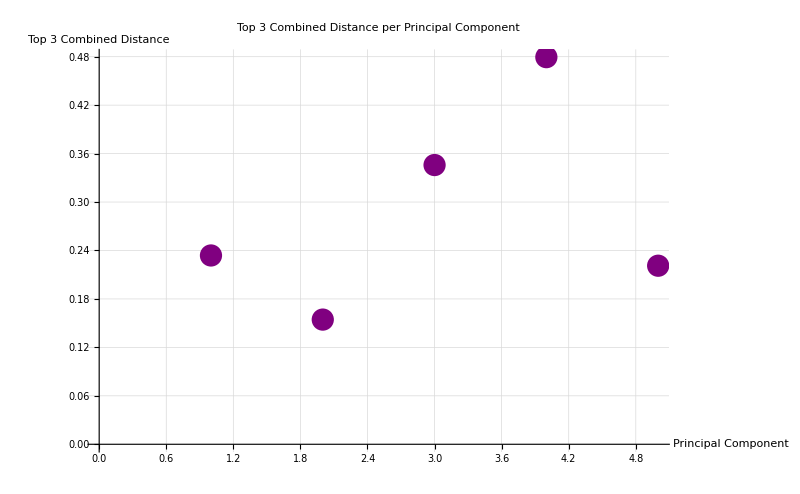
{-Graphics-,{PC 1,T3 Combined Distance: 0.234} | {PC 2,T3 Combined Distance: 0.154} | {PC 3,T3 Combined Distance: 0.346} | {PC 4,T3 Combined Distance: 0.479} | {PC 5,T3 Combined Distance: 0.221}
neglectful (0.271) | friendly (0.194) | passive (0.362) | fragile (0.535) | lustful (0.229)
uninterested (0.284) | amiable (0.228) | timid (0.410) | sensitive (0.547) | molestful (0.240)
negligent (0.294) | outgoing (0.243) | shy (0.416) | emotional (0.549) | pedophilic (0.260)
apathetic (0.302) | sociable (0.245) | reserved (0.423) | introverted (0.558) | violent (0.319)
indifferent (0.349) | extroverted (0.270) | modest (0.480) | compassionate (0.559) | torturous (0.325)
irresponsible (0.369) | fun-loving (0.291) | humble (0.489) | solitary (0.562) | murderous (0.326)
unsystematic (0.383) | adventurous spirit (0.306) | fragile (0.495) | humble (0.577) | cannibalistic (0.413)
jerk (0.392) | energetic (0.313) | introverted (0.511) | sympathetic (0.595) | sadistic (0.450)
turbulent (0.397) | generous (0.326) | indecisive (0.539) | submissive (0.597) | greedy (0.468)
hostile (0.403) | supportive (0.342) | cautious (0.546) | modest (0.598) | corrupt (0.546)
... | ... | ... | ... | ...
persuasive (1.560) | rational (1.494) | narcissistic (1.527) | innovative thinker (1.390) | serious (1.371)
cooperative leader (1.561) | utilitarian (1.496) | zealous (1.528) | innovative (1.399) | traditional (1.379)
organized (1.567) | logical (1.514) | vindictive (1.532) | resourceful (1.404) | dour (1.388)
scientific (1.579) | realistic (1.515) | sadistic (1.534) | grounded (1.439) | charismatic (1.391)
practical dreamer (1.592) | analytical (1.518) | corrupt (1.539) | irresponsible (1.460) | rigid thinker (1.393)
trustworthy (1.609) | perfectionist (1.527) | greedy (1.552) | practical (1.478) | confident (1.400)
diplomatic negotiator (1.612) | aloof (1.532) | fanatical (1.556) | disorganized (1.484) | showy (1.413)
planner (1.621) | loner (1.555) | bold (1.564) | practical thinker (1.527) | perfectionist (1.427)
visionary pragmatist (1.642) | rigid thinker (1.569) | competitive (1.585) | unsystematic (1.538) | conventional (1.433)
strategic thinker (1.693) | unsympathetic (1.632) | vengeful (1.611) | spontaneous (1.539) | arrogant (1.447),-Graphics-}

```mathematica
numComponents=5;
{plot2D,gridOutput,combinedDistancePlot}=PCAAnalysis[standardized,personalityNames,numComponents]
```

```mathematica
gridOutput
```

{PC 1,T3 Combined Distance: 0.234} | {PC 2,T3 Combined Distance: 0.154} | {PC 3,T3 Combined Distance: 0.346} | {PC 4,T3 Combined Distance: 0.479} | {PC 5,T3 Combined Distance: 0.221}
neglectful (0.271) | friendly (0.194) | passive (0.362) | fragile (0.535) | lustful (0.229)
uninterested (0.284) | amiable (0.228) | timid (0.410) | sensitive (0.547) | molestful (0.240)
negligent (0.294) | outgoing (0.243) | shy (0.416) | emotional (0.549) | pedophilic (0.260)
apathetic (0.302) | sociable (0.245) | reserved (0.423) | introverted (0.558) | violent (0.319)
indifferent (0.349) | extroverted (0.270) | modest (0.480) | compassionate (0.559) | torturous (0.325)
irresponsible (0.369) | fun-loving (0.291) | humble (0.489) | solitary (0.562) | murderous (0.326)
unsystematic (0.383) | adventurous spirit (0.306) | fragile (0.495) | humble (0.577) | cannibalistic (0.413)
jerk (0.392) | energetic (0.313) | introverted (0.511) | sympathetic (0.595) | sadistic (0.450)
turbulent (0.397) | generous (0.326) | indecisive (0.539) | submissive (0.597) | greedy (0.468)
hostile (0.403) | supportive (0.342) | cautious (0.546) | modest (0.598) | corrupt (0.546)
... | ... | ... | ... | ...
persuasive (1.560) | rational (1.494) | narcissistic (1.527) | innovative thinker (1.390) | serious (1.371)
cooperative leader (1.561) | utilitarian (1.496) | zealous (1.528) | innovative (1.399) | traditional (1.379)
organized (1.567) | logical (1.514) | vindictive (1.532) | resourceful (1.404) | dour (1.388)
scientific (1.579) | realistic (1.515) | sadistic (1.534) | grounded (1.439) | charismatic (1.391)
practical dreamer (1.592) | analytical (1.518) | corrupt (1.539) | irresponsible (1.460) | rigid thinker (1.393)
trustworthy (1.609) | perfectionist (1.527) | greedy (1.552) | practical (1.478) | confident (1.400)
diplomatic negotiator (1.612) | aloof (1.532) | fanatical (1.556) | disorganized (1.484) | showy (1.413)
planner (1.621) | loner (1.555) | bold (1.564) | practical thinker (1.527) | perfectionist (1.427)
visionary pragmatist (1.642) | rigid thinker (1.569) | competitive (1.585) | unsystematic (1.538) | conventional (1.433)
strategic thinker (1.693) | unsympathetic (1.632) | vengeful (1.611) | spontaneous (1.539) | arrogant (1.447)

## Find Most Orthogonal Personalities

```mathematica
FindOrthogonalVectors[vectors_List,threshold_:1*^-3]:=Block[{n,dotProducts,orthogonalPairs,heatmap},
n=Length[vectors];
dotProducts=Table[Dot[vectors[[i]],vectors[[j]]],{i,n},{j,n}];
orthogonalPairs=Select[Flatten[Table[{i,j,dotProducts[[i,j]]},{i,n},{j,i,n}],1],Abs[#[[3]]]<threshold&];

heatmap=ArrayPlot[Abs[dotProducts],ColorFunction->"Rainbow",ColorFunctionScaling->True,PlotLabel->"Dot Product Heatmap",FrameTicks->{Automatic,Automatic},ImageSize->500,AspectRatio->1];
{orthogonalPairs,heatmap,Abs[dotProducts]}
]
```

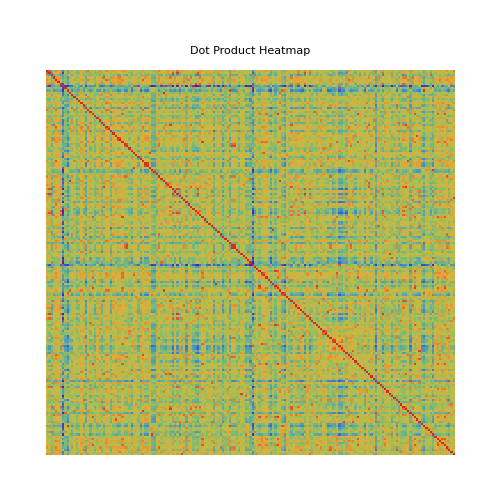

```mathematica
data = allPersMeanOfDiff[[All,18]];
{orthogonalPairs,heatmap,pairwiseLoss}=FindOrthogonalVectors[data,.5];
heatmap
```

```mathematica
MapAndSortOrthogonalPairs[orthogonalPairs_List,personalityNames_List]:=Module[{sortedPairs},
sortedPairs=SortBy[orthogonalPairs,Abs[#[[3]]]&];
Table[{personalityNames[[pair[[1]]]],personalityNames[[pair[[2]]]],pair[[3]]},

{pair,sortedPairs}]]

mappedAndSortedPairs=MapAndSortOrthogonalPairs[orthogonalPairs,personalityNames];

mappedAndSortedPairs[[;;10]]//TableForm
mappedAndSortedPairs//Dimensions
```

analytical | fun-loving | 0.0749698
analytical | laid-back | 0.1035
fun-loving | logical | 0.120681
analytical | energetic | 0.122776
analytical | friendly | 0.12908
analytical | sociable | 0.131065
analytical | irresponsible | 0.132409
analytical | disorganized | 0.133687
laid-back | logical | 0.134135
analytical | unsystematic | 0.136804

{2436,3}

### Visualize Top Orthogonal Vectors

```mathematica
pcaVectors=Transpose[PrincipalComponents[Transpose[standardized]]];
reducedManual=standardized.Transpose[eigenvectors[[;;3]]];

sortedPairs=SortBy[orthogonalPairs,Abs[#[[3]]]&];

topOrthogonalVectors=sortedPairs[[;;10, {1,2}]]//Flatten//DeleteDuplicates;

topOrthogonalVectors=topOrthogonalVectors[[;;3]];
reducedVectorsToPlot=reducedManual[[topOrthogonalVectors]];

vectorNames=personalityNames[[topOrthogonalVectors]];
vectorColors={Red,Green,Blue, Purple, Orange, Yellow, Black};  

vectorGraphics=Table[{vectorColors[[i]],Arrow[{{0,0,0},reducedVectorsToPlot[[i]]}]},{i,Length[reducedVectorsToPlot]}];

textGraphics=Table[Text[Style[vectorNames[[i]],Bold,FontSize->12],reducedVectorsToPlot[[i]]+{0.1,0.1,.1}],{i,Length[reducedVectorsToPlot]}];

Graphics3D[
{vectorGraphics,textGraphics},
Axes->False,
PlotLabel->"Top 3 Most Orthogonal Vectors in Reduced 3D Space",
Boxed->True, 
BoxRatios->{1,1,1},
 ImageSize->500]
```

-Graphics3D-

```mathematica
nextOrthogonalVectors=sortedPairs[[;;80,{1,2}]]//Flatten//DeleteDuplicates;
nextOrthogonalVectors =Complement[nextOrthogonalVectors, topOrthogonalVectors];

reducedNextVectorsToPlot=reducedManual[[nextOrthogonalVectors]];

nextVectorNames=personalityNames[[nextOrthogonalVectors]];

vectorGraphics=Table[{vectorColors[[i]],Arrow[{{0,0,0},reducedVectorsToPlot[[i]]}]},{i,Length[reducedVectorsToPlot]}];

textGraphics=Table[Text[Style[vectorNames[[i]],Bold,FontSize->12],reducedVectorsToPlot[[i]]+{0.1,0.1,0.1}],{i,Length[reducedVectorsToPlot]}];

nextVectorGraphics=Table[{Gray,Dashed,Arrowheads[Medium],Arrow[{{0,0,0},reducedNextVectorsToPlot[[i]]}]},{i,Length[reducedNextVectorsToPlot]}];

nextTextGraphics=Table[Text[Style[nextVectorNames[[i]],FontSize->10,Gray],reducedNextVectorsToPlot[[i]]+{0.1,0.1,0.1}],{i,Length[reducedNextVectorsToPlot]}];

Graphics3D[
{vectorGraphics,textGraphics,nextVectorGraphics,nextTextGraphics},
Axes->False,
AxesLabel->{"PC1","PC2","PC3"},
PlotLabel->"Top 3 Most Orthogonal Vectors in Reduced 3D Space",
Boxed->True,
BoxRatios->{1,1,1},
ImageSize->600]
```

-Graphics3D-